```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
assoc=Get["wickSATdata.txt"];
```

```mathematica
Keys @ assoc
```

{numIterations,derivAccuracy,matrNoise,wrapParams,timeStep,numBools,numParams,threshold,solProbEvo,expectedEnergyEvo,paramEvo,spectrumSize,spectrum,spectrumDegeneracy,solStateSpecInd,specEvo}

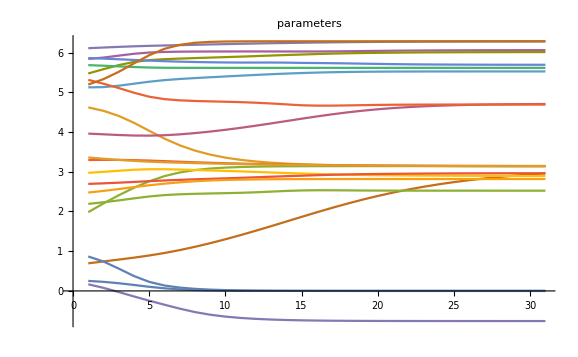

```mathematica
ListLinePlot[ assoc["paramEvo"],PlotLabel-> "parameters"]
```

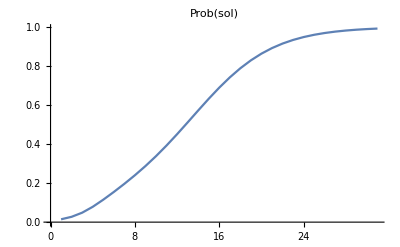

```mathematica
ListLinePlot[
	assoc["solProbEvo"], PlotLabel-> "Prob(sol)"
]
```

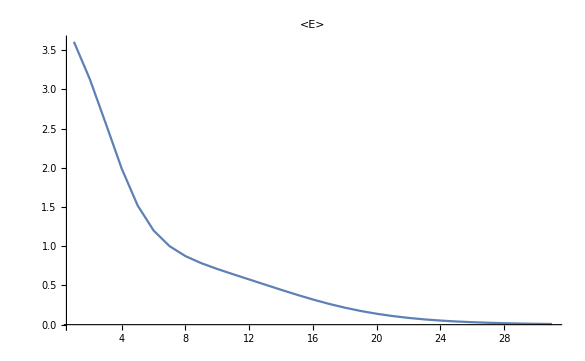

```mathematica
ListLinePlot[
	assoc["expectedEnergyEvo"], PlotLabel -> "<E>",
	PlotRange-> All
]
```